## Kapitola 1 - Mathematica, stručný úvod

Seznámení se základy používání systému Mathematica, úvod do syntaxe, ovládání, vizualizace a základy programování.

## Ovládání

Soubor v Mathematice (nazývá se notebook) se dělí na tzv. buňky (po pravé straně můžete vidět grafické prvky, znázorňující jednotlivé buňky). Buňky mohou být různého typu a mohou být hierarchicky řazeny - např. buňka typu "nadpis" pod sebou uchovává všechny buňky, které patří do dané kapitoly.
Dvojklikem na "závorku" (na pravé straně notebooku), reprezentující buňku, nebo skupinu buněk, lze tyto "zavírat" a "otevírat".

Základní dva typy buněk jsou "vstupní" (input) a "výstupní" (output). Vstupní buňky obsahují uživatelem zadané (vyhodnotitelné) příkazy - tyto se vyhodnotí stiskem Shift+Enter (nebo samotný Enter na numerické klávesnici). Výsledek vyhodnocení se zobrazí v následující výstupní buňce, viz příklad:

```mathematica
1+1
```

2

Do kódu (příkazu) je možné vkádat komentář pomocí "(*" a "*)".

```mathematica
1 + 1 (* Velmi jednoduchý příklad pro začátek *)
```

2

## Základy syntaxe

Základní matematické výrazy mají klasickou syntaxi (+-*/), závorky se píší stejně jako v matematice - "()". Priority operátorů jsou interpretovány správně, tak jak jsme z matematiky zvyklí.

```mathematica
3+4/2
```

5

V jedné vstupní buňce je možné kombinovat více příkazů, ty se oddělí koncem řádku.

```mathematica
4/2
(5+7)/3
```

2

4

Lze se také odkazovat na předchozí výsledek pomocí znaku "%".

```mathematica
1+1
```

2

```mathematica
%*5
```

10

Argumenty funkcí se zapisují do hranatých závorek "[]". Mathematica je case - sensitive systém a všechny vestavěné funkce začínají velkým písmenem (to ulehčuje odlišení vlastních funkcí od vestavěných).

```mathematica
Sin[3.14]
```

0.00159265

Veškeré výpočty probíhají (implicitně) v absolutní přesnosti - to znamená, že všechny výsledky jsou zcela přesné.

```mathematica
Sin[Pi/3]
```

(√3)/2

Funkcí "N" můžeme každý výraz převést do číselného vyjádření (přijdeme tím o absolutní přesnost).

```mathematica
N[Sin[Pi/3]]
```

0.866025

Je možné zadat počet desetinných míst.

```mathematica
N[Pi,100]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

Často používaný je postfixový zápis.

```mathematica
Sin[Pi/3]//N
```

0.866025

Cokoliv je možné ukládat do proměnných.

```mathematica
x=Pi/3
```

π/3

Proměnné lze používat jako argumenty funkcí.

```mathematica
Sin[x]
```

(√3)/2

Pomoci znaku středník ";" je možné potlačit vypsání výstupu.

```mathematica
x=Pi/3; (* Přiřazení, bez výpisu na obrazovku *)
```

```mathematica
Sin[x]
```

(√3)/2

Další důležitou strukturou jsou seznamy ...
Zadávají se do složených závorek "{}" a mohou mít zcela libovolnou strukturu (seznam seznamů apod.)

```mathematica
{1,2,3,4}
```

{1,2,3,4}

```mathematica
{{1,2,3},{4,5,6}}
```

{{1,2,3},{4,5,6}}

Na seznamy je možné aplikovat různé funkce.

```mathematica
seznam={Pi/4,Pi/3,Pi/2,Pi}
```

{π/4,π/3,π/2,π}

```mathematica
Sin[seznam]
```

{1/(√2),(√3)/2,1,0}

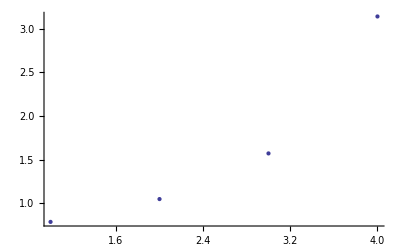

```mathematica
ListPlot[seznam]
```

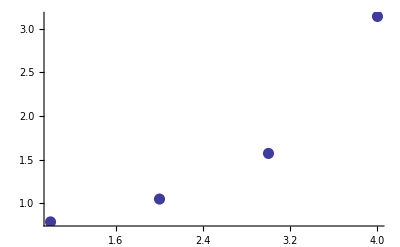

```mathematica
ListPlot[seznam,PlotStyle->PointSize[0.02]]
```

Vybírání prvků ze seznamu (indexace) se provádí pomocí dvojitých složených závorek "[[" a "]]".

```mathematica
seznam[[1]]
```

π/4

Seznamy je možné vytvářet buď přímo zápisem hodnot do závorek (viz výše), nebo pomocí dalších příkazů jako "Table", "Array", atd.

```mathematica
seznam2=Table[i^2,{i,1,10}]
```

{1,4,9,16,25,36,49,64,81,100}

Prvky seznamu mohou být zase seznamy (zde dvouprvkový seznam s hodnotou iterátoru a jeho druhou mocninou).

```mathematica
seznam3=Table[{i,i^2},{i,1,10}]
```

{{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

Výsledek si můžeme zobrazit ve formě matice.

```mathematica
MatrixForm[seznam3]
```

(1 | 1
2 | 4
3 | 9
4 | 16
5 | 25
6 | 36
7 | 49
8 | 64
9 | 81
10 | 100)

Velmi užitečná věc jsou tzv. lambda funkce (nepojmenované funkce), a mapovací operátory - znáte např. z Lispu.

Máme seznam a chceme na každý prvek aplikovat nějakou funkci - např. třetí mocninu.

```mathematica
seznam
```

{π/4,π/3,π/2,π}

Použijeme mapovací operátor a lambda funkci.

```mathematica
Map[Function[x,x^3],seznam]
```

{π^3/64,π^3/27,π^3/8,π^3}

To je sice celkem čitelný příklad, ale v praxi se používá častěji zkrácená varianta zápisu lambda funkce - argument lambda funkce se označuje "#" a celá funkce se ukončuje znakem "&".

```mathematica
Map[#^3&,seznam]
```

{π^3/64,π^3/27,π^3/8,π^3}

Pokud chceme ušetřit ještě pár znaků, můžeme použít zkrácenou (v praxi též často používanou) verzi zápisu mapovacího operátoru "/@".

```mathematica
#^3&/@seznam
```

{π^3/64,π^3/27,π^3/8,π^3}

Data můžeme téměř libovolně vizualizovat.

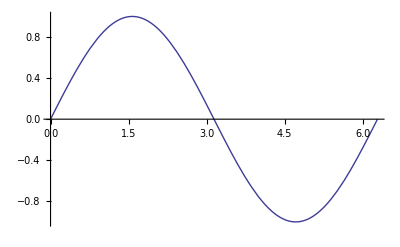

```mathematica
Plot[Sin[x],{x,0,2Pi}]
```

```mathematica
Plot3D[Sin[x^2+y^2],{x,-Pi,Pi},{y,-Pi,Pi}]
```

-Graphics3D-

```mathematica
ContourPlot[Sin[x^2+y^2],{x,-Pi,Pi},{y,-Pi,Pi}]
```

-Graphics-

Grafy mohou být interaktivní.

```mathematica
Manipulate[Plot[Sin[a x+b],{x,0,2π}],{a,1,10},{b,1,10}]
```

Interaktivní mohou být vlastně libovolně výrazy.

```mathematica
Manipulate[Expand[(a+b)^n],{n,2,10,1}]
```

Můžeme definovat vlastní funkce. Detaily syntaxe - podtržítka "_" a odložené přiřazení ":=" zatím nebudeme vysvětlovat. Plyne to z vlastnosti vyhodnocování výrazů, rule - based programování apod., zatím nám bude stačit, že to takhle funguje.

```mathematica
f[x_]:=1/(1+E^-x)
```

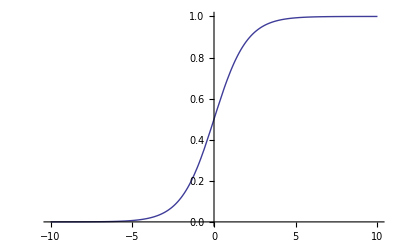

```mathematica
Plot[f[x],{x,-10,10}]
```

Výrazy můžeme zadávat v "hezké" formě - zlomek se dělá Ctrl + /, Mocnina Ctrl + 6 (na klávese "6" je znak "^" - tím se to dobře pamatuje). Řecká písmena a další speciální symboly se zadávají pomocí escape: např. [esc] Pi [esc], Eulerovo číslo [esc] ee [esc]

```mathematica
f[x_]:=1/(1+ⅇ^-x)
```

I vzhled grafu lze ovlivňovat.

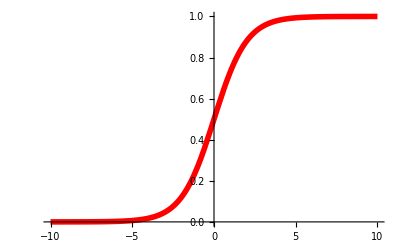

```mathematica
Plot[f[x],{x,-10,10},PlotStyle->{Thickness[0.01],Red}]
```

Funkce s více parametry.

```mathematica
g[x_,λ_]:=1/(1+ⅇ^(-λ x))
```

Lze vykreslit více grafů do jednoho obrázku - jednotlivé funkce se potom zadávají do seznamu.

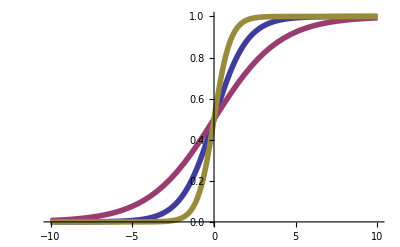

```mathematica
Plot[{g[x,1],g[x,0.5],g[x,2]},{x,-10,10},PlotStyle->Thickness[0.01]]
```

## Programování

### Rule - based programování

Velkou část systému Mathematica tvoří tzv. rule - based programování. Obecně Mathematica kombinuje všechna běžná programovací paradigmata - funkcionální, procedurální, rekurzivní, rule - based styl ...

V rule-based programování používáme tzv. vzory. Ty umožňují zastoupit celou řadu výrazů:

_ - (podtržítko) jeden výskyt
__ - (dvě podtržítka) jeden nebo více výskytů
___ - (tři podtržítka) libovolný počet výskytů (i nula)
_h - výraz s hlavičkou "h"

Nejprve se podíváme na tzv. hlavičku výrazu. Každý výraz - symbol, seznam, číslo, všechno... má svoji hlavičku. Tu můžeme zjistit pomocí příkazu (funkce) "Head".

```mathematica
Head[z]
```

Symbol

```mathematica
Head[1]
```

Integer

```mathematica
Head[3.14]
```

Real

To bylo snadné - teď pozor, zbystřit - jakou hlavičku má například volání funkce?

```mathematica
Head[fce[z]]
```

fce

Prima, je to název funkce ... teď třeba seznam.

```mathematica
Head[{1,2,3,a,b,c}]
```

List

Hlavičkou seznamu je "List". To je celkem logické, protože "List" je vlastně funkce a jejími argumenty jsou prvky samotného seznamu. Výrazy si můžeme zobrazovat ve své vnitřní formě pomocí funkce "FullForm" - takže se teď podíváme na seznam ještě jednou.

```mathematica
FullForm[{1,2,3,a,b,c}]
```

List[1,2,3,a,b,c]

Tady je to vidět, opravdu je to funkce s parametry odpovídajícími prvkům seznamu.

Pomocí funkce "Apply" (zkrácený zápis : "@@") lze zaměňovat hlavičky výrazů.

```mathematica
Apply[fce,{1,2,3,a,b,c}]
```

fce[1,2,3,a,b,c]

```mathematica
fce@@{1,2,3,a,b,c}
```

fce[1,2,3,a,b,c]

Je libo například sečíst prvky seznamu? No prosím :

```mathematica
Plus@@{1,2,3,a,b,c}
```

6+a+b+c

Už víme něco o hlavičce, takže můžeme začít používat pravidla. Pokusíme se vybrat ze zadaného seznamu výrazů takové, které odpovídají zadanému vzoru.

Vybereme všechna volání funkce "r" :

```mathematica
Cases[{r[a],r[1],r[a,b],s[a],s[a,b],a,3},_r]
```

{r[a],r[1],r[a,b]}

Všechny funkce (na názvu nezáleží) se dvěma parametry (vzpomeňte - podtržítko odpovídá právě jednomu výskytu "něčeho"):

```mathematica
Cases[{r[a],r[1],r[a,b],s[a],s[a,b],a,3},_[_,_]]
```

{r[a,b],s[a,b]}

Teď třeba všechny funkce s jedním parametrem :

```mathematica
Cases[{r[a],r[1],r[a,b],s[a],s[a,b],a,3},_[_]]
```

{r[a],r[1],s[a]}

Zkusíme si zpracovat nějaký větší výraz.

```mathematica
vyraz=Sin[z]+z^(a+b)-Exp[z^w]+1/z^2
```

-ⅇ^(z^w)+1/z^2+z^(a+b)+Sin[z]

Jeho vnitřní reprezentace :

```mathematica
FullForm[vyraz]
```

Plus[Times[-1,Power[E,Power[z,w]]],Power[z,-2],Power[z,Plus[a,b]],Sin[z]]

Vybereme všechny mocniny z výrazu (1/z^2 je reprezentované jako z^-2):

```mathematica
Cases[vyraz,_^_]
```

{1/z^2,z^(a+b)}

Teď si zkusíme vzory pojmenovat a použít - pokud dáme před podtržítko název, vznikne pojmenovaný vzor (teď si vzpomeňte na definici vlastní funkce, viz výše - vzpomínáte na podtržítko v názvu parametru? To je přesně ono).

Když už máme vzory pojmenované, tak s nimi můžeme pracovat. Použijeme tzv. přepisovací pravidlo - zapisuje se pomocí "šipky" - pomlčka a "většítko".

Všechny mocniny nahradíme vlastní funkcí "funkce".

```mathematica
Cases[vyraz,a_^b_->funkce[a,b]]
```

{funkce[z,-2],funkce[z,a+b]}

Pro aplikaci přepisovacích pravidel se používají převážně funkce "Replace" (zkráceně "/.") a "ReplaceAll" (zkráceně "//.").

Rozdíl je v tom, že ReplaceAll aplikuje zadaná pravidla tak dlouho, dokud se výraz mění, zatímco Replace je aplikuje pouze jednou.

```mathematica
{1,2,3,a,b,c,d,a+b}/.{a->BAF}
```

{1,2,3,BAF,b,c,d,b+BAF}

Můžeme tak kompletně měnit výrazy, demonstrační příklad - nahradíme název funkce a její argumenty :

```mathematica
funkce1[parametr1]+funkce2[parametr2]/.{a_[b_]->b[a]}
```

parametr1[funkce1]+parametr2[funkce2]

Zkusme si nadefinovat Fibonacciho posloupnost pomocí pravidel :

```mathematica
fibo[10]/.
{fibo[1]->1,fibo[2]->2,fibo[a_]->fibo[a-1]+fibo[a-2]}
```

fibo[8]+fibo[9]

Vidíte, že se aplikovala pravidla a původní výraz se transformoval na volání dvou funkcí (generujicí posloupnost).

Protože ale chceme vypočítat výsledné číslo Fibonacciho posloupnosti, potřebujeme aplikovat pravidla stále dokola, dokud to jde - použijeme ReplaceAll (zkráceně "//.").

```mathematica
fibo[10]//.
{fibo[1]->1,fibo[2]->2,fibo[a_]->fibo[a-1]+fibo[a-2]}
```

89

U vzoru můžeme definovat také implicitní hodnoty. V následujícím příkladu hledáme výskyty funkce "fce" s jedním, dvěma, nebo třemi parametry - pravidlo je jedno, ale díky implicitním hodnotám jsou parametry nepovinné (stejně jako např. c++ si chybějící parametr nahradí svojí implicitní hodnotou.

Volání funkce se transformuje na seznam argumentů - chybějící argumenty jsou nahrazeny implicitní hodnotou.

```mathematica
Cases[{fce[a,b,c],fce[a,b],fce[a]},fce[a_:1,b_:2,c_:3]->{a,b,c}]
```

{{a,b,c},{a,b,3},{a,2,3}}

Definice funkce, která implicitně počítá druhou mocninu a pokud je potřeba (je zadán druhý parametr), vypočítá mocninu obecnou.

```mathematica
mocnina[x_,y_:2]:=x^y;
```

```mathematica
mocnina[3]
```

9

```mathematica
mocnina[10]
```

100

```mathematica
mocnina[2,8]
```

256

Můžeme se podívat, jak je naše funkce v Mathematice definována :

```mathematica
?mocnina
```

To odpovídá naší definici. Můžeme jít ještě dál a podívat se na konkrétní pravidla, která realizuje.

```mathematica
DownValues[mocnina]
```

{HoldPattern[mocnina[x_,y_:2]]:>x^y}

Aha! Je to pravidlo - nepatrně se odlišuje od toho co známe - ta podivná šipka s dvojtečkou představuje tzv. odložené pravidlo - tj. pravidlo, které se expanduje až ve chvíli aplikace.

Teď zkombinujme pojmenované vzory a pravidla. Vytvoříme pravidlo, které nahradí funkci "fce" počtem jejich parametrů. Vzor pojmenujeme "p" - funkce "Length" vrací počet prvků seznamu - v našem případě tedy počet argumentů.

```mathematica
{fce[a,b],fce[a,b,c],fce[1],fce[1,2,3,4]}/.p:fce[___]->Length[p]
```

{0,0,0,0}

Vidíme, že to nezafungovalo tak, jak bychom si představovali. To je právě tím, že se samotné pravidlo vyhodnotilo a pak teprve aplikovalo na zadaný seznam. Takže tady právě využijeme již zmíněné odložené pravidlo (zapisuje se znaky dvojtečka a "většítko" - ":>")

```mathematica
{fce[a,b],fce[a,b,c],fce[1],fce[1,2,3,4]}/.p:fce[___]:>Length[p]
```

{2,3,1,4}

Už to funguje ...

Na závěr si ukážeme kombinaci předchozího + ještě navíc tzv. opakující se vzory - to se zapisuje znaky ".." a znamená, že se daný vzor opakuje libovolně - krát.

Implementujeme funkci pro RLE kompresi pomocí rule - based programování.

Vidíme rekurzivní aplikaci funkce definované pomocí opakujících se vzorů. První argument odpovídá libovolnému výskytu "čehokoliv" (tzv. zbytek - vzpomeňte na Prolog - celkem typické), druhý argument je potom opakující se vzor "x_", to znamená množina stejných výrazů (čísel, znaků, apod.). Funguje to podobně jako  tzv. "žravé" regularní výrazy v Perlu - argument "same" pak obsahuje seznam stejných hodnot. Délka tohoto seznamu je pak jeden z výsledků RLE.

```mathematica
rle[{rest___,same:(x_)..}]:=Append[rle[{rest}],{x,Length[{same}]}];
rle[{}]={};
```

```mathematica
rle[{1,2,2,2,a,a,a,a,a,b,b,3,4,4,4,4}]
```

{{1,1},{2,3},{a,5},{b,2},{3,1},{4,4}}

## Prohlášení

Tento text je součástí bakalářské práce Adama Činčury “Demonstrační aplikace pro podporu kurzu neuronových sítí” na FEL ČVUT 2011. Vznikl úpravou textu Petra Chlumského.